# NG4P13 SOM

Выполнила  студентка 2 курса  5 группы
Кадакова Надежда
10.06.2017

## Ex.1

Задание: Исследовать аппроксимирующие способности ИНС Кохонена (Self-Organizing Map). В файле NG17P13Problem.xlsx приведены обучающие наборы:

страница «Clout» — фрагмент поверхности тора, вложенный в трехмерное пространство;

страница «Torus» — тор, вложенный в трехмерное пространство;

страница «ProjectivePlane» — проективная плоскость, вложенная в шестимерное пространство.

Со страницы «Clout» загрузить обучающий набор. Изобразить его черным цветом (см. Рис.1). Создать двухмерную сеть Кохонена размером 10×10. Разместить её нейроны в узлах равномерной сетки, расположенной на горизонтальной плоскости: (x,y,0), где -0.5⩽x,y⩽0.5, и изобразить сеть Кохонена синим цветом (см. Рис.1). Запрограммировать функцию, по заданным номеру узла сети Кохонена и точке фазового пространства строящую красную стрелку из узла в точку (см. Рис.1).

-Graphics-

Устанавливаем директорию

```mathematica
SetDirectory[NotebookDirectory[]]
```

I:\Nadzeya Kadakova

Импортируем  точки из  xlsx файла

```mathematica
Clout=Import["NG17P13Problem.xlsx",{"Sheets","Clout"}];
```

Создаем сеть Кохонена размером 10*10 с тремя координатами в каждом узле.
Идем от -0.5 до 0.5. Для этого задаем шаг  (#1-1)/10. #1 идет по строкам, #2 по столбцам.

```mathematica
CohanNet=Array[{-0.5+(#1-1)/10,-0.5+(#2-1)/10,0}&,{10,10}];
```

Отобразим точки:

```mathematica
phasespace = Graphics3D[{RGBColor[0,0,0],Point@Clout}, Boxed -> False, PlotRange -> Automatic]
```

-Graphics3D-

Array работает построчно. Также как и Line. Поэтому мы можем соединить только точки в строках.

```mathematica
Fig0=Graphics3D[Dynamic@{Hue[0.7],Line[CohanNet]},AspectRatio->1, Boxed->False]
```

-Graphics3D-

Поэтому здесь мы транспонируем матрицу, чтобы столбцы стали строками. теперь мы можем соединить и столбцы.
Еще это можно сделать при помощи функций Rectangle, Polygon.

```mathematica
Fig1=Graphics3D[Dynamic@{Hue[0.7],Line[CohanNetᵀ]},AspectRatio->1, Boxed->False]
```

-Graphics3D-

```mathematica
Show[Fig0,Fig1]
```

-Graphics3D-

Зададим узлы сети Кохонена.

```mathematica
Fig2 = Graphics3D[Dynamic@{Hue[0.7], PointSize -> 0.03, Point[Flatten[CohanNet, 1]]},AspectRatio->1, Boxed->False]
```

-Graphics3D-

```mathematica
Show[Fig0,Fig1,Fig2]
```

-Graphics3D-

Номер узла - это индекс в матрице. Матрица индексов двумерная. Нужно написать функцию, которая будет строить по заданному индексу и точке фазового пространства стрелку.

```mathematica
CohanNet[[{9,2}[[1]], {9,2}[[2]]]]
```

{0.3,-0.4,0}

```mathematica
ArrowNear[Neuroind_, PhaseSpacePoint_] := Graphics3D[Dynamic@{Hue[1], Arrow[{CohanNet⟦Neuroind⟦1⟧, Neuroind⟦2⟧⟧, PhaseSpacePoint}]}];
```

```mathematica
ArrowNear[{9,2},Clout⟦3⟧]
```

-Graphics3D-

## Ex.2

Написать процедуру обучения двухмерной сети Кохонена. Обучить сеть, созданную в п.1, на обучающем наборе «Clout». Процесс обучения визуализировать (см. Рис.2).

Обучение сети Кохонена происходит следит следующим образом. первым делом мы для любой точки фазового пространства находим ближайший узел в сети. Мы будем искать индексы, так как это проще. Как только ближайший узел найден, начинаем тянуть сетку за этот узел в данном направлении. 
Первым делом, мы берем свою сетку. прибавляем к ней

```mathematica
FindNearestNeuroInd[Near_] := Flatten[{Quotient[#, 10, 1] + 1, Mod[#, 10, 1]} & /@ Nearest[Flatten[CohanNet, 1] -> "Index", Near], 1];
```

```mathematica
Quotient[100, 10,1]
```

9

Несколько отличительных особенностей сети Кохонена заключается в том, что скорость обучения (“сила, с которой мы тянем”) сначала большая, а потом уменьшается. Во-вторых, у точки есть окрестность, сильно реагирующая на перемещение. И сначала она большая, а потом также уменьшается.

Задаем значения из книжки.

Задаем значения из книжки.

```mathematica
(*начальная окрестность *)
σstart=3;
(*сигма на последней итерации - конечная окрестность*)
σit=1.25;
(*скорость обучения - начальная*)
ηstart=0.1;
(*скорость обучения - конечная*)
ηit=0.01;
(*количество итераций*)
it=1000;
(*время*)
t=0;
(*коэффициент изменения параметров - с пары*)
σspeed=-it/Log[σit/σstart];
ηspeed=-it/Log[ηit/ηstart];

NB[dist_]:=Exp[-dist^2/(2 σ^2)];
```

```mathematica
CohanNet=Array[{-0.5+(#1-1)/10,-0.5+(#2-1)/10,0}&,{10,10}];
```

Первым делом, мы берем свою сетку. прибавляем к ней

```mathematica
Do[(*вычисляем окрестность, вычисляем скорость обучения*)
σ=σstart Exp[-t/σspeed];
η=ηstart Exp[-t/ηspeed];
(*Выбираем случайную точку *)
Near=RandomChoice@Clout;
(*Ищем ближайший индекс нейрона*)
Neuro=FindNearestNeuroInd[Near];
(*Мы должны сместить нашу сеть. Для этого находим матрицу смещения. От выбранной точки, отнимаем всю сеть кохонена. Как бы из каждого узла строим вектор. Чтобы определить направление, по которому наша сеть потянется. (MAP)
Теперь нужно полученное умножить на функцию расстояния. Ф-ция расстояния показывает насколько сильно нам нужно потянуть узел. (Расстоние - внутреннее. в сети). Это реализуется с помощью MapIndexed.*)CohanNet=MapIndexed[#1NB[Plus@@Abs[Neuro-#2]]&,Map[Near-#&,CohanNet,{2}],{2}]η+CohanNet;
t++;
(*Dynamic везде использую для того, чтобы моментально отображать изменения.*)

FinishDynamic[];
,it];
(*отображаем*)
CohanNetWork=Dynamic@Show[phasespace,Fig0,Fig1,Fig2,ArrowNear[Neuro,Near],Boxed->False];(*обнуляем время*)t=0;
```

```mathematica
CohanNetWork
```

Вычислить первые две компоненты обучающего набора «Clout». В плоскости, натянутой на первые две главные компоненты, параллельно главным компонентам построить равномерную сетку размером 10×10, описывающую проекцию данного обучающего набора на данную плоскость. Изобразить её зеленым цветом (см. Рис.3).

```mathematica
(*вычисляем компоненты при помощи метода главных компонент.*)
```

```mathematica
Vecs=PrincipalComponents[Clout]⟦1;;2⟧;
```

```mathematica
(*сетка опять строится с помощью оператора array*)
```

```mathematica
PlaneCohanNet=Array[-0.45(Normalize@Vecs⟦2⟧+Normalize@((Vecs⟦1⟧×Vecs⟦2⟧)×Vecs⟦2⟧))(*посчитали начальную точку*)+(#1-1)/10(*шаг*)Normalize@Vecs⟦2⟧(*первый вектор*)+(#2-1)/10 Normalize@((Vecs⟦1⟧×Vecs⟦2⟧)×Vecs⟦2⟧)&,{10,10}];
```

```mathematica
(*для того, чтобы сетку задать равномерно, необходимо из афинной системы координат, где оси совпадают с направлением компонент, перейти в ортагональную. Для этого найдем векторное произведение двух векторов. тогда получится вектор, перпендикулярный данным (вертикально), а потом еще раз умножаем векторно.*)
```

```mathematica
Show[phasespace,Graphics3D[Dynamic@{Hue[1],Arrow[{{0,0,0},Normalize@Vecs⟦1⟧}]}],Graphics3D[Dynamic@{Hue[0.7],Arrow[{{0,0,0},Normalize@Vecs⟦2⟧}]}]]
```

-Graphics3D-

```mathematica
(*а сетка строится точно также как и в предыдущем задании*)
```

```mathematica
Fig00=Graphics3D[Dynamic@{Green,Line[PlaneCohanNet]}];
Fig10=Graphics3D[Dynamic@{Green,Line[PlaneCohanNetᵀ]}];
Fig20=Graphics3D[Dynamic@{Green,PointSize-> 0.01,Point[Flatten[PlaneCohanNet,1]]}];
ArrowNear[Neuroind_,Near_]:=Graphics3D[Dynamic@{Hue[1],Arrow[{CohanNet⟦Neuroind⟦1⟧,Neuroind⟦2⟧⟧,Near}]}];
```

```mathematica
Dynamic@Show[Fig00,Fig10,Fig20,phasespace,Graphics3D[Dynamic@{Hue[1],Arrow[{{0,0,0},Normalize@Vecs⟦1⟧}]}],Graphics3D[Dynamic@{Hue[0.7],Arrow[{{0,0,0},Normalize@Vecs⟦2⟧}]}],Boxed->False]
```

Рис 3.  Первые две главные компоненты и двумерная сеть Кохонена

## Ex.3

Написать процедуру обучения одномерной сети Кохонена. Обучить данную сеть на обучающем наборе «Clout». Процесс обучения визуализовать (см. Рис.4).

“сворачиваем нашу нитку с узлами(одномерную сеть кохонена) в клубок”

```mathematica
Cohan1Net=RandomPoint[Sphere[{0,0,0},0.3],20];
```

Так как сеть одномерная, транспонирование нам уже не нужно

```mathematica
Fig01=Graphics3D[Dynamic@{Hue[0.7],Line[Cohan1Net]}]
```

-Graphics3D-

```mathematica
Fig21=Graphics3D[Dynamic@{Hue[0.7],PointSize-> 0.013,Point[Cohan1Net]}]
```

-Graphics3D-

```mathematica
phasespace1=Graphics3D[Point@Clout,Boxed->False,PlotRange->Automatic]
```

-Graphics3D-

```mathematica
Find1NearestNeuroInd[Near_]:=First@Nearest[Cohan1Net->"Index",Near]
```

```mathematica
(*т.к. сеть одномерная, то и индекс одномерный*)
```

```mathematica
Arrow1Near[Neuroind_,Near_]:=Graphics3D[Dynamic@{Hue[1],Arrow[{Cohan1Net⟦Neuroind⟧,Near}]}]
```

Параметры можно перезадать

```mathematica
σstart=3;
σit=1.25;
ηstart=0.5;
ηit=0.01;
it=1000;
t=0;
σspeed=-it/Log[σit/σstart];
ηspeed=-it/Log[ηit/ηstart];

NB[dist_]:=Exp[-dist^2/(2 σ^2)];
```

```mathematica
Do[σ=σstart Exp[-t/σspeed];
η=ηstart Exp[-t/ηspeed];
Near=RandomChoice@Clout;
Neuro=Find1NearestNeuroInd[Near];
Cohan1Net=MapIndexed[#1NB[Plus@@Abs[Neuro-#2]]&,Near-#&/@Cohan1Net,{1}]η+Cohan1Net;
t++;
FinishDynamic[];
,1000];Cohan1NetWork=Dynamic@Show[phasespace,Fig01,Fig21,phasespace1,Arrow1Near[Neuro,Near],Boxed->False];t=0;
```

$Aborted

```mathematica
Cohan1NetWork
```

## Ex.4

Для каждой обученной сети Кохонена (из пп.2 и 4) оценить её качество, вычислив для этого: (а) среднее расстояние сети до объектов, используемых для обучения, и (б) стандартное (средне-квадратичное) отклонение расстояний (разброс). Для каждой сети построить диаграмму зависимости вешнего расстояния между узлами сети от внутреннего расстояния (см. Рис.5) и вычислить коэффициент корреляции. Полученные результаты объяснить.

a) вычисляем расстояние до claut для двухмерной и одномерной сети.

```mathematica
mean2d=Mean[EuclideanDistance[CohanNet⟦#⟦1⟧,#⟦2⟧⟧&@FindNearestNeuroInd[#],#]&/@Clout]
mean1d=Mean[EuclideanDistance[Cohan1Net⟦First@#⟧&@FindNearestNeuroInd[#],#]&/@Clout]
```

0.251051

1.89544

б) стандартное отклонение

```mathematica
squaremean2d=StandardDeviation[EuclideanDistance[CohanNet⟦#⟦1⟧,#⟦2⟧⟧&@FindNearestNeuroInd[#],#]&/@Clout]
```

0.176473

```mathematica
squaremean1d=StandardDeviation[EuclideanDistance[Cohan1Net⟦First@#⟧&@FindNearestNeuroInd[#],#]&/@Clout]
```

0.698069

```mathematica
(*считаем внутреннее расстояние между индексами. у нас 20 узлов, поэтому range = 20*)
```

```mathematica
innerdistance1d=DistanceMatrix[Range[20]];
(*считаем внешнее расстояние между кооринатами.*)
outerdistance1d=DistanceMatrix[Cohan1Net];
res1d=MapThread[List,{Flatten[outerdistance1d,1],Flatten[innerdistance1d,1]}];
```

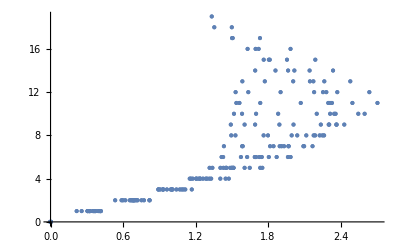

```mathematica
ListPlot@res1d
```

```mathematica
ind2d=Table[{i,j},{i,10},{j,10}];
```

```mathematica
(*ищем расстояние между узлами сети*)
```

```mathematica
innerdistance2d=Flatten[Table[Plus@@Abs[ind2d⟦i,j⟧-ind2d⟦k,l⟧],{i,10},{j,10},{k,10},{l,10}],1];
outerdistance2d=DistanceMatrix[Flatten[CohanNet,1]];
res2d=MapThread[List,{Flatten[outerdistance2d,1],Flatten[innerdistance2d,2]}];
```

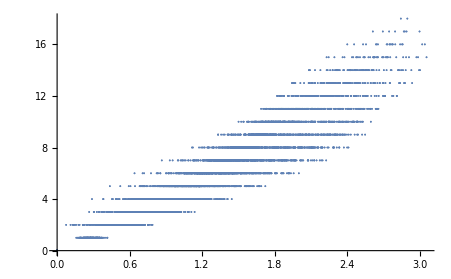

```mathematica
ListPlot@res2d
```

```mathematica
Correlation[res1d]⟦1,2⟧
```

0.762501

```mathematica
Correlation[res2d]⟦1,2⟧
```

0.932957

Два экземпляра двухмерной сети Кохонена размером 18×18 (см. п.2) обучить на наборах «Torus» и «ProjectivePlane». Первый экземпляр изобразить на рисунке. В обоих случаях исследовать расстояние между граничными узлами сети. Результат объяснить и визуализовать (см. Рис.5).

```mathematica
Torus=Import["NG17P13Problem.xlsx",{"Sheets","Torus"}];
ProjectivePlane=Import["NG17P13Problem.xlsx",{"Sheets","ProjectivePlane"}];
```

```mathematica
CohanTorusNet=Array[{-0.5+(#1-1)/18,-0.7,-0.5+(#2-1)/18}&,{18,18}];
Fig02=Graphics3D[Dynamic@{Hue[0.7],Line[CohanTorusNet]}];
Fig12=Graphics3D[Dynamic@{Hue[0.7],Line[CohanTorusNetᵀ]}];
Fig22=Graphics3D[Dynamic@{Hue[0.7],PointSize-> 0.01,Point[Flatten[CohanTorusNet,1]]}];
phasespace2=Graphics3D[Point@Torus,Boxed->False,PlotRange->Automatic];
FindNearestTorusNeuroInd[Near_]:=Flatten[{Quotient[#,18,1]+1,Mod[#,18,1]}&/@Nearest[Flatten[CohanTorusNet,1]->"Index",Near],1];
ArrowTorusNear[Neuroind_,Near_]:=Graphics3D[Dynamic@{Hue[1],Arrow[{CohanTorusNet⟦Neuroind⟦1⟧,Neuroind⟦2⟧⟧,Near}]}];
```

```mathematica
CohanPlaneNet=Array[{-0.5+(#1-1)/18,-0.5+(#2-1)/18,0,0,0,0}&,{18,18}];

FindNearestPlaneNeuroInd[Near_]:=Flatten[{Quotient[#,18,1]+1,Mod[#,18,1]}&/@Nearest[Flatten[CohanPlaneNet,1]->"Index",Near],1];
```

```mathematica
σstart=3;
σit=1.25;
ηstart=0.1;
ηit=0.01;
it=2000;
t=0;
σspeed=-it/Log[σit/σstart];
ηspeed=-it/Log[ηit/ηstart];

NB[dist_]:=Exp[-dist^2/(2 σ^2)];
```

```mathematica
Do[σ=σstart Exp[-t/σspeed];
η=ηstart ;
Near=RandomChoice@ProjectivePlane;
Neuro=FindNearestPlaneNeuroInd[Near];
CohanPlaneNet=MapIndexed[#1NB[Plus@@Abs[Neuro-#2]]&,Map[Near-#&,CohanPlaneNet,{2}],{2}]η+CohanPlaneNet;
t++;
FinishDynamic[];
,it];t=0;
```

```mathematica
Do[σ=σstart Exp[-t/σspeed];
η=ηstart ;
Near=RandomChoice@Torus;
Neuro=FindNearestTorusNeuroInd[Near];
CohanTorusNet=MapIndexed[#1NB[Plus@@Abs[Neuro-#2]]&,Map[Near-#&,CohanTorusNet,{2}],{2}]η+CohanTorusNet;
t++;
FinishDynamic[];
,it];CohanTorusNetWork=Dynamic@Show[phasespace2,Fig02,Fig12,Fig22,ArrowTorusNear[Neuro,Near],Boxed->False];t=0;
```

```mathematica
CohanTorusNetWork
```

Пример использования сети Кохонена - задача кластеризации данных об успеваемости студентов одной из студенческих учебных групп

-Graphics-

-Graphics-

Распределение примеров должно осуществляться строго по 4 кластерам.В качестве входных переменных используем x1–x7, переменная x8 не будет использоваться для обучения, однако информация о ее значениях будет задействована в ходе кластерного анализа.Таким образом, структурно сеть будет состоять из единственного слоя нейронов, имеющего 7 входов и 4 выхода

-Graphics-

Выполним линейную нормализацию аналоговых значений входных переменных выборки в пределах[0, 1] по соотношению (3.1).Дискретные значения опишем следующим образом :
 –пол студента : 0–женский, 1–мужской;

–наличие всех зачетов : 0–нет, 1–да.Результаты нормализации представлены в табл.2.

Проинициализируем все 28 весовых коэффициентов нейронной сети значениями, представленными в табл.3, с учетом ограничения (2).

http://neuronus.com/theory/961-nejronnye-seti-kokhonena.html интересная статейка.